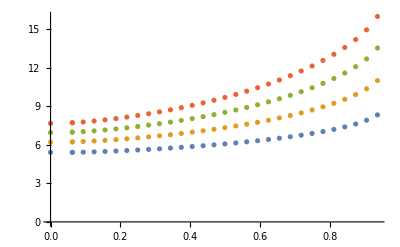

```mathematica
a={{0,5.404137},{0.062500,5.405383},{0.062500,5.405383},{0.093750,5.421956},{0.125000,5.445248},{0.156250,5.474318},{0.187500,5.508337},{0.218750,5.546740},{0.250000,5.589143},{0.281250,5.635300},{0.312500,5.685068},{0.343750,5.738391},{0.375000,5.795289},{0.406250,5.855854},{0.437500,5.920246},{0.468750,5.988696},{0.500000,6.061509},{0.531250,6.139073},{0.562500,6.221867},{0.593750,6.310485},{0.625000,6.405654},{0.656250,6.508282},{0.687500,6.619513},{0.718750,6.740824},{0.750000,6.874191},{0.781250,7.022362},{0.812500,7.189386},{0.843750,7.381690},{0.875000,7.610636},{0.906250,7.900093},{0.937500,8.318570}};
a2={{0,6.200516},{0.062500,6.217142},{0.062500,6.217142},{0.093750,6.248318},{0.125000,6.289166},{0.156250,6.338720},{0.187500,6.395887},{0.218750,6.459933},{0.250000,6.530395},{0.281250,6.607010},{0.312500,6.689671},{0.343750,6.778398},{0.375000,6.873327},{0.406250,6.974695},{0.437500,7.082840},{0.468750,7.198195},{0.500000,7.321298},{0.531250,7.452792},{0.562500,7.593444},{0.593750,7.744161},{0.625000,7.906028},{0.656250,8.080359},{0.687500,8.268778},{0.718750,8.473358},{0.750000,8.696849},{0.781250,8.943083},{0.812500,9.217728},{0.843750,9.529845},{0.875000,9.895548},{0.906250,10.348672},{0.937500,10.987524}};
a3={{0,6.941366},{0.062500,6.973810},{0.062500,6.973810},{0.093750,7.019542},{0.125000,7.077676},{0.156250,7.147267},{0.187500,7.226995},{0.218750,7.315989},{0.250000,7.413726},{0.281250,7.519935},{0.312500,7.634548},{0.343750,7.757662},{0.375000,7.889519},{0.406250,8.030493},{0.437500,8.181083},{0.468750,8.341909},{0.500000,8.513715},{0.531250,8.697377},{0.562500,8.893913},{0.593750,9.104509},{0.625000,9.330558},{0.656250,9.573725},{0.687500,9.836046},{0.718750,10.120103},{0.750000,10.429313},{0.781250,10.768449},{0.812500,11.144617},{0.843750,11.569254},{0.875000,12.062832},{0.906250,12.668469},{0.937500,13.512209}};
a4={{0,7.657825},{0.062500,7.706031},{0.062500,7.706031},{0.093750,7.766178},{0.125000,7.841394},{0.156250,7.930760},{0.187500,8.032732},{0.218750,8.146310},{0.250000,8.270916},{0.281250,8.406278},{0.312500,8.552368},{0.343750,8.709358},{0.375000,8.877596},{0.406250,9.057585},{0.437500,9.249979},{0.468750,9.455576},{0.500000,9.675316},{0.531250,9.910292},{0.562500,10.161759},{0.593750,10.431163},{0.625000,10.720182},{0.656250,11.030802},{0.687500,11.365432},{0.718750,11.727119},{0.750000,12.119891},{0.781250,12.549393},{0.812500,13.024074},{0.843750,13.557628},{0.875000,14.174701},{0.906250,14.927396},{0.937500,15.968860}};
ListPlot[{a,a2,a3,a4}]
```

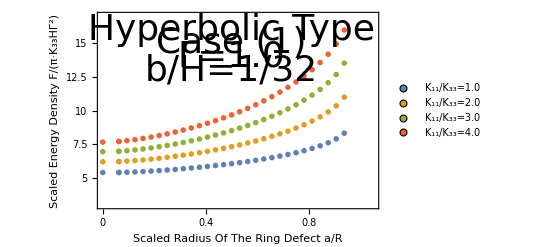

```mathematica
ListPlot[{a,a2,a3,a4},PlotStyle->PointSize[0.01], Frame->{True, True, True, True}, FrameTicks->{{{5,7.5,10,12.5,15},None},{{0,0.2, 0.4, 0.6, 0.8,1.0},None}}, PlotRange->{{0,1.05},{3,17}},FrameLabel->{{"Scaled Energy Density F/(π·K_33HΓ^2)", None},{"Scaled Radius Of The Ring Defect a/R", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"K_11/K_33=1.0","K_11/K_33=2.0","K_11/K_33=3.0","K_11/K_33=4.0"},LegendMarkers->{{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12}}],{Left, Top}],Epilog->{Text[Style["Hyperbolic Type",Directive[Black,36]],{0.5,16}],Text[Style["Case (1)",Directive[Black,36]],{0.5,15}],Text[Style["Γ=1.0",Directive[Black,36]],{0.5,14.0}],Text[Style["b/H=1/32",Directive[Black,36]],{0.5,13}]}]
```

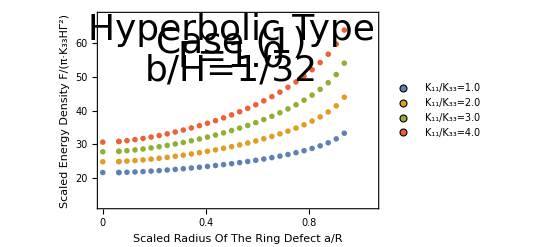

```mathematica
aa=a*Table[{1,4},{i,0,30}];
aa2=a2*Table[{1,4},{i,0,30}];
aa3=a3*Table[{1,4},{i,0,30}];
aa4=a4*Table[{1,4},{i,0,30}];
ListPlot[{aa,aa2,aa3,aa4},PlotStyle->PointSize[0.01], Frame->{True, True, True, True}, FrameTicks->{{{20,30,40,50,60},None},{{0,0.2, 0.4, 0.6, 0.8,1.0},None}}, PlotRange->{{0,1.05},{12,68}},FrameLabel->{{"Scaled Energy Density F/(π·K_33HΓ^2)", None},{"Scaled Radius Of The Ring Defect a/R", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"K_11/K_33=1.0","K_11/K_33=2.0","K_11/K_33=3.0","K_11/K_33=4.0"},LegendMarkers->{{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12}}],{Left, Top}],Epilog->{Text[Style["Hyperbolic Type",Directive[Black,36]],{0.5,64}],Text[Style["Case (1)",Directive[Black,36]],{0.5,60}],Text[Style["Γ=1.0",Directive[Black,36]],{0.5,56}],Text[Style["b/H=1/32",Directive[Black,36]],{0.5,52}]}]
```